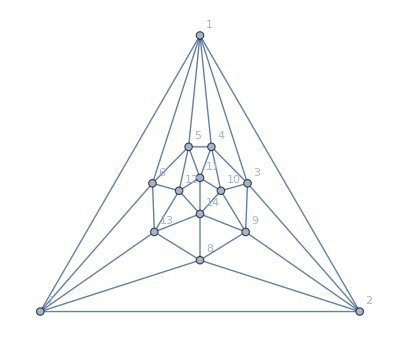

```mathematica
pl1=Graph[plantri[[2]],VertexLabels->"Name", GraphLayout->"TutteEmbedding"]
```

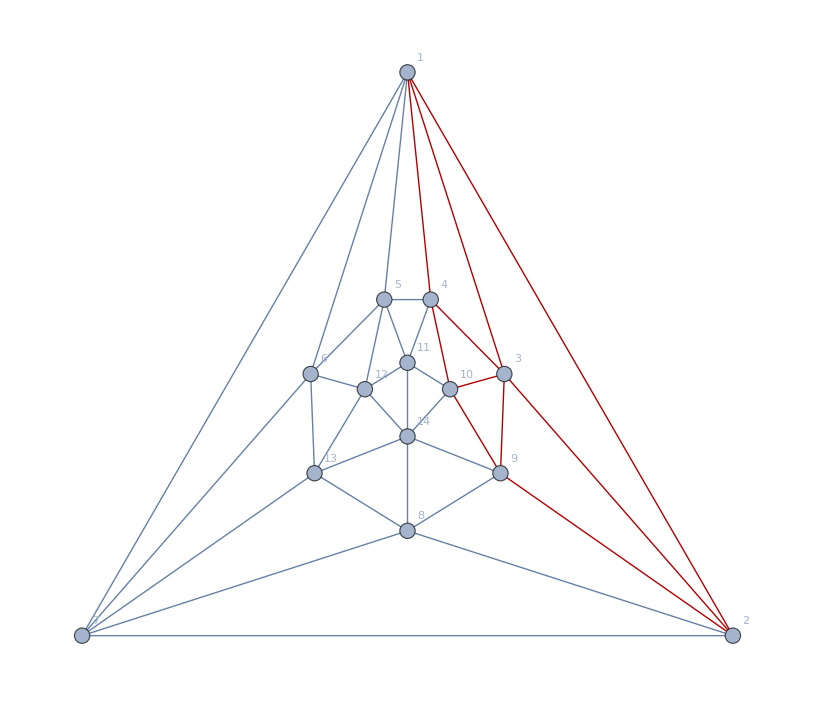

```mathematica
pl2=Graph[pl1,GraphHighlight->Join[Table[k<->3,{k,{2,9,10,4,1}}],{1<->2,9<->2,10<->9,10<->4,4<->1}]]
```

```mathematica
ffpl2=FindFullFormula[pl2];
```

```mathematica
Length[ffpl2]
```

854693

```mathematica
ChromaticPolynomial[pl2,4]/24//Factor
```

20

```mathematica
HighlightSymbol[s_]:=Row[Map[If[#=="x",Style[#,Red],If[MemberQ[{"1","2","9","a","4"},#],Style[#,Blue],#]]&,StringPartition[SymbolName[s],1]]]
```

```mathematica
HighlightSymbol[v1ex25adx479cx68b]
```

v1ex25adx479cx68b

```mathematica
NotGood[s_]:=SetsToSymbol2[Sort[Map[Sort,SymbolToSets[ Symbol[StringJoin[Select[StringPartition[SymbolName[s],1],!MemberQ[{"1","2","9","a","4"},#]&]]]]],First[#1]<First[#2]&]]
```

```mathematica
Good[s_]:=SetsToSymbol2[Select[Sort[Map[Sort,SymbolToSets[ Symbol [StringJoin[Select[StringPartition[SymbolName[s],1],MemberQ[{"v","x","1","2","9","a","4"},#]&]]]]],First[#1]<First[#2]&],#≠{}&]]
```

```mathematica
DrawSolution[s_]:=Block[{colors={},sets,base={Blue,Red,Green,Yellow},i},
sets=SymbolToSets[s];
For[i=1,i≤Length[sets],i++,
Table[
AppendTo[colors,v->base[[i]]]
,
{v,sets[[i]]}
]
];
Graph[pl2,VertexStyle-> colors,ImageSize->300,VertexSize->.6]
]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

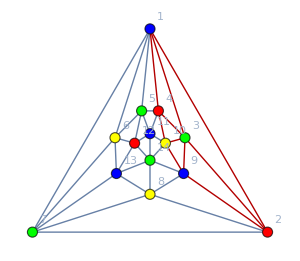
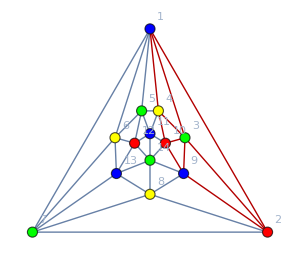
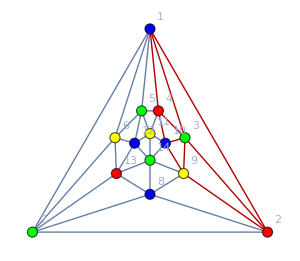
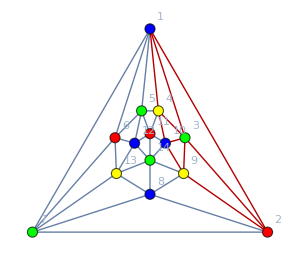
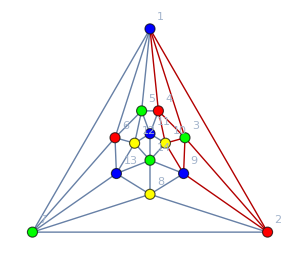
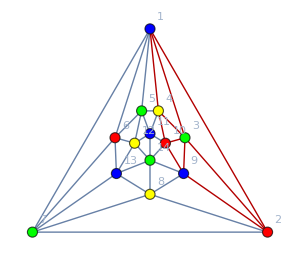
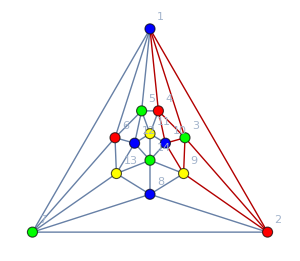
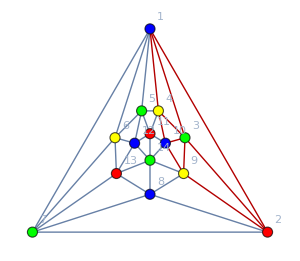
v357ex68xbdxc | 2 | v19x24xa | v19bdx24cx357ex68a | -Graphics-
v357ex68xbdxc | 2 | v19x2ax4 | v19bdx2acx357ex468 | -Graphics-
v357ex6bx8cxd | 2 | v1ax24x9 | v18acx24dx357ex69b | -Graphics-
v357ex6bx8cxd | 2 | v1ax2x49 | v18acx26bx357ex49d | -Graphics-
v357ex6x8cxbd | 2 | v19x24xa | v19bdx246x357ex8ac | -Graphics-
v357ex6x8cxbd | 2 | v19x2ax4 | v19bdx26ax357ex48c | -Graphics-
v357ex6x8cxbd | 2 | v1ax24x9 | v18acx246x357ex9bd | -Graphics-
v357ex6x8cxbd | 2 | v1ax2x49 | v18acx2bdx357ex469 | -Graphics-
v357x6ex8cxbd | 2 | v19x24xa | v19bdx246ex357x8ac | -Graphics-
v357x6ex8cxbd | 2 | v1ax24x9 | v18acx246ex357x9bd | -Graphics-
v358x6ex7cxbd | 2 | v19x24xa | v19bdx246ex358x7ac | -Graphics-
v35dx6ex7bx8c | 2 | v1ax24x9 | v18acx246ex35dx79b | -Graphics-
v368bx5dx7cxe | 2 | v1x2ax49 | v1ex25adx368bx479c | -Graphics-
v368bx5dx7exc | 2 | v19x2ax4 | v19cx25adx368bx47e | -Graphics-
v368bx5ex7cxd | 2 | v1ax2x49 | v1adx25ex368bx479c | -Graphics-
v36ex5dx7cx8b | 2 | v1x2ax49 | v18bx25adx36ex479c | -Graphics-
v37bx5dx6ex8c | 2 | v1ax24x9 | v18acx246ex37bx59d | -Graphics-
v37cx58x6exbd | 2 | v19x24xa | v19bdx246ex37cx58a | -Graphics-
v38cx57x6exbd | 2 | v19x24xa | v19bdx246ex38cx57a | -Graphics-
v3bdx57x6ex8c | 2 | v1ax24x9 | v18acx246ex3bdx579 | -Graphics-

```mathematica
pl2gen=TableForm[
Map[Framed[TableForm[#]]&,
GatherBy[
Map[{NotGood[#],With[{g=Good[#]},TableForm[{StringCount[SymbolName[g],"x"],g}, TableDirections->Row]],HighlightSymbol[#],DrawSolution[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]],TableDepth->1]
```

```mathematica
GatherBy[
Map[{NotGood[#],Good[#],HighlightSymbol[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{{{v357ex68xbdxc,v19x24xa,v19bdx24cx357ex68a},{v357ex68xbdxc,v19x2ax4,v19bdx2acx357ex468}},{{v357ex6bx8cxd,v1ax24x9,v18acx24dx357ex69b},{v357ex6bx8cxd,v1ax2x49,v18acx26bx357ex49d}},{{v357ex6x8cxbd,v19x24xa,v19bdx246x357ex8ac},{v357ex6x8cxbd,v19x2ax4,v19bdx26ax357ex48c},{v357ex6x8cxbd,v1ax24x9,v18acx246x357ex9bd},{v357ex6x8cxbd,v1ax2x49,v18acx2bdx357ex469}},{{v357x6ex8cxbd,v19x24xa,v19bdx246ex357x8ac},{v357x6ex8cxbd,v1ax24x9,v18acx246ex357x9bd}},{{v358x6ex7cxbd,v19x24xa,v19bdx246ex358x7ac}},{{v35dx6ex7bx8c,v1ax24x9,v18acx246ex35dx79b}},{{v368bx5dx7cxe,v1x2ax49,v1ex25adx368bx479c}},{{v368bx5dx7exc,v19x2ax4,v19cx25adx368bx47e}},{{v368bx5ex7cxd,v1ax2x49,v1adx25ex368bx479c}},{{v36ex5dx7cx8b,v1x2ax49,v18bx25adx36ex479c}},{{v37bx5dx6ex8c,v1ax24x9,v18acx246ex37bx59d}},{{v37cx58x6exbd,v19x24xa,v19bdx246ex37cx58a}},{{v38cx57x6exbd,v19x24xa,v19bdx246ex38cx57a}},{{v3bdx57x6ex8c,v1ax24x9,v18acx246ex3bdx579}}}

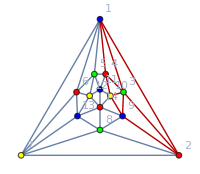

```mathematica
DrawSolution[v19bdx246ex358x7ac]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

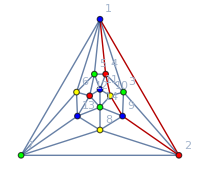
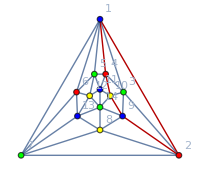
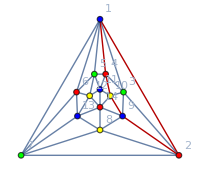
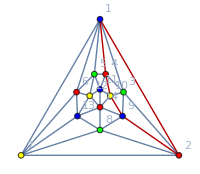
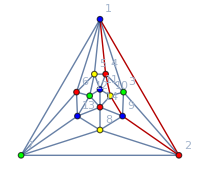
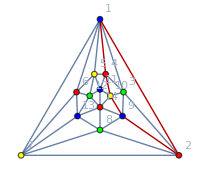
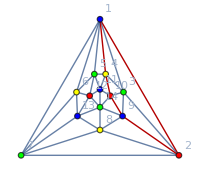
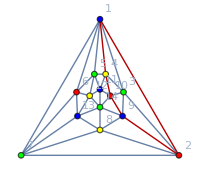
2 | v19x24xa | v357ex68xbdxc | v19bdx24cx357ex68a | -Graphics-
2 | v19x24xa | v357ex6x8cxbd | v19bdx246x357ex8ac | -Graphics-
2 | v19x24xa | v357x6ex8cxbd | v19bdx246ex357x8ac | -Graphics-
2 | v19x24xa | v358x6ex7cxbd | v19bdx246ex358x7ac | -Graphics-
2 | v19x24xa | v37cx58x6exbd | v19bdx246ex37cx58a | -Graphics-
2 | v19x24xa | v38cx57x6exbd | v19bdx246ex38cx57a | -Graphics-
2 | v19x2ax4 | v357ex68xbdxc | v19bdx2acx357ex468 | -Graphics-
2 | v19x2ax4 | v357ex6x8cxbd | v19bdx26ax357ex48c | -Graphics-
2 | v19x2ax4 | v368bx5dx7exc | v19cx25adx368bx47e | -Graphics-
2 | v1ax24x9 | v357ex6bx8cxd | v18acx24dx357ex69b | -Graphics-
2 | v1ax24x9 | v357ex6x8cxbd | v18acx246x357ex9bd | -Graphics-
2 | v1ax24x9 | v357x6ex8cxbd | v18acx246ex357x9bd | -Graphics-
2 | v1ax24x9 | v35dx6ex7bx8c | v18acx246ex35dx79b | -Graphics-
2 | v1ax24x9 | v37bx5dx6ex8c | v18acx246ex37bx59d | -Graphics-
2 | v1ax24x9 | v3bdx57x6ex8c | v18acx246ex3bdx579 | -Graphics-
2 | v1ax2x49 | v357ex6bx8cxd | v18acx26bx357ex49d | -Graphics-
2 | v1ax2x49 | v357ex6x8cxbd | v18acx2bdx357ex469 | -Graphics-
2 | v1ax2x49 | v368bx5ex7cxd | v1adx25ex368bx479c | -Graphics-
2 | v1x2ax49 | v368bx5dx7cxe | v1ex25adx368bx479c | -Graphics-
2 | v1x2ax49 | v36ex5dx7cx8b | v18bx25adx36ex479c | -Graphics-

```mathematica
TableForm[
Map[Framed[TableForm[#]]&,
GatherBy[
Map[{With[{g=Good[#]},TableForm[{StringCount[SymbolName[g],"x"],g}, TableDirections->Row]],NotGood[#],HighlightSymbol[#],DrawSolution[#]}&,Select[ffpl2,StringCount[SymbolName[#],"x"]==3&]]//Sort,
First]],TableDepth->1]
```